# Advanced Basics of Mathematica Grammar 2011 (easy/medium)

### Replacements

Very important equations arising in the study on quantum integrable models are the so called Y-system equations:

Y_j(u+1)Y_j(u-1)=(1+Y_(j-1)(u))(1+Y_(j+1)(u))   for j=1,...,n      and        Y_j(u)=0 for j≤0 or j≥ n+1.

By considering a few different n's convince yourself that they imply that

Y_j(u+n+3)=Y_(n-j+1)(u)

Hint: Understand

```mathematica
f[5]/.f[a_]:>f[a-1]+a/;a>0
```

5+f[4]

```mathematica
f[5]//.f[a_]:>f[a-1]+a
```

-2147123200+f[-65531]

```mathematica
f[5]//.f[a_]:>f[a-1]+a/;a>0
```

15+f[0]

#### Solution

```mathematica
n=4;
j=2;
Y[j_,u_]:=0/;j≤0∨j>n;
Y[j,n+3]/Y[n-j+1,0]//.Y[j_,u_]:>((1+Y[j-1,u-1])(1+Y[j+1,u-1]))/Y[j,u-2]/;u>0//Simplify
```

1

### Conjugate

Consider some generic complex function such as

```mathematica
s=(Exp[I kx ]+Exp[2I ky ])
```

ⅇ^(ⅈ kx)+ⅇ^(2 ⅈ ky)

Sometimes we might want Mathematica to conjugate such expressions assuming all variables to be real unless told otherwise. That is we would like a function conj such that

```mathematica
conj[s]s//FullSimplify
```

(ⅇ^(ⅈ kx)+ⅇ^(2 ⅈ ky)) conj[ⅇ^(ⅈ kx)+ⅇ^(2 ⅈ ky)]

should yield

2 (1+Cos[kx-2 ky])

Create such function. Hint: Run

```mathematica
FullForm/@{Exp[I kx],A+B I,-2I}
```

{Power[E,Times[Complex[0,1],kx]],Plus[A,Times[Complex[0,1],B]],Complex[0,-2]}

#### Solution

```mathematica
conj=#/.Complex[α_,β_]->α-β I&;
```

### Tensor Products

How to proceed to get the following nice implementation of the tensor product:

```mathematica
({{a, b}, {c, d}})⊗ ({{α, β, γ}, {ϵ, ϕ, ρ}})//MatrixForm
```

{{a,b},{c,d}}⊗{{α,β,γ},{ϵ,ϕ,ρ}}

#### Solution

```mathematica
CircleTimes=KroneckerDelta
```

### Simplify

FullSimplify measures the complexity of the expression, which it tries to reduce then, in some very special way. It uses the function LeafCount . In some cases this leads to a really strange behavior:

Run

```mathematica
FullSimplify[Sin[3(u+π)]+Cos[5(u+π)]]
```

Cos[5 (π+u)]+Sin[3 (π+u)]

and

```mathematica
FullSimplify[Sin[3(u+π)]-Cos[5(u+π)]]
```

Cos[5 u]-Sin[3 u]

Apply TreeForm  to both functions (with and without FullSimplify). Do it also for what you would like the output of the first line to be. Same for LeafCount. Mathematica wants to minimize LeafCount. Why doesn't Mathematica simplify the first line as we would?

Try to find some other examples where FullSimplify "fails". 

The LeadCount function can be replaced by a user defined function. You can invent your own measure of complexity which you like. Hive several examples of your own ComplexityCount function and use it to simplify the expression you found.

Create your own function Simpy which simplifies expressions with 3π etc inside trigonometric functions in a more human way.

Hint: Functions which you might find useful are: TrigToExp, ExpandAll, ...

#### Solution

```mathematica
firstcase={Sin[3(u+π)]-Cos[5(u+π)],Cos[5u]-Cos[3u]};
secondcase={Sin[3(u+π)]+Cos[5(u+π)],-Cos[5u]-Cos[3u]};
```

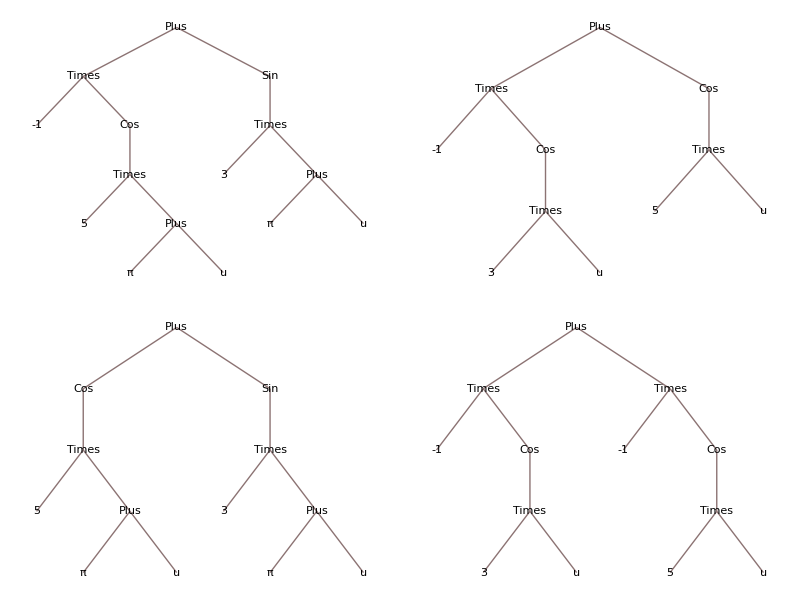

```mathematica
{TreeForm/@firstcase,TreeForm/@secondcase}//TableForm
```

```mathematica
LeafCount/@firstcase
LeafCount/@secondcase
```

{15,11}

{13,13}

Examples:

```mathematica
Sin[3(u+π)]+Cos[5(u+π)]//TrigExpand//FullSimplify
Sin[3(u+π)]+Cos[5(u+π)]//ExpandAll
Sin[3(u+π)]+Cos[5(u+π)]//TrigReduce
```

-Cos[5 u]-Sin[3 u]

-Cos[5 u]-Sin[3 u]

-Cos[5 u]-Sin[3 u]

### Sqrt killer

Define a function which will bring the expression with a single square roots in denominator to the canonical form, that is

(...+√(...))/((...+√(...))...(...+√(...)))→...+... √(...)

#### Solution

```mathematica
KSqr:=Block[{tmp},tmp=Factor[#];Collect[Numerator[tmp] (Denominator[tmp]/.√a_:>-√a),√_,Factor]/Collect[Denominator[tmp] (Denominator[tmp]/.√a_:>-√a),√_,Factor]]&;
```

```mathematica
(a+√a1)/((a1+a2 √b)(a2+a3 √b1))//KSqr
```

(a1^(3/2) (a2-a3 √b1)+a1 (a a2-a a3 √b1)+√b (-a a2^2+√a1 (-a2^2+a2 a3 √b1)+a a2 a3 √b1))/((a1^2-a2^2 b) (a2^2-a3^2 b1))

### Memorizer

Define a function which will solve

F_n==F_(n-1)+1/F_(n-2)     with      F_1=F_2=1.2

Plot the sequence log(F_n) with n=1,...,1000 (should take less than one second)

#### Solution

```mathematica
ClearAll[F];
F[1]=F[2]=1.2;
F[n_]:=F[n]=F[n-1]+1/F[n-2];
```

```mathematica
ListPlot@Table[Log[F[i]],{i,1000}]//Timing
```

{0.156192,-Graphics-}

### Puzzles*

*(from http : // richardwiseman.wordpress.com/ , solutions proposed here taken from the comment box and were given by Simon)

Puzzle 1: How can you place the arithmetical signs ‘+’ and ‘-’ between the consecutive numbers 123456789 so that the end result is 100?  
Try to come up with a code to solve this problem. Also, decode the sollowing solution*

```mathematica
Do[If[ToExpression[str=StringJoin[Riffle[Characters["123456789"],i]]]==100,Print["100=",str]],{i,Tuples[{"+","-",""},8]}]
```

Puzzle 2: Yesterday I went shopping and picked up four items. When I got to the till, the cashier added the price of the four items together and the bill was £7.11. I then noticed that I would get exactly the same total if I were to multiply the four prices. How much did each of the items cost? 
Note: What the puzzle should say is: “Find integers a,b,c,d such that a+b+c+d = 711 and a b c d = 711 000 000.”
Again, try to come up with a code to solve this problem and/or decode the solution*

```mathematica
Select[IntegerPartitions[711,{4}],Times@@#==711000000&]
```

#### Solution given in the text